```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\mathematica

```mathematica
Pi * 14^2
```

196 π

```mathematica
N[Pi * 14^2]
```

615.752

```mathematica
pi * 14^2
```

196 pi

```mathematica
Round[37.5]
```

38

```mathematica
Round[37.2]
```

37

```mathematica
Round[37.2, 3]
```

36

```mathematica
Mod[7, 4]
```

3

```mathematica
Quotient[7, 4]
```

1

```mathematica
28 + 14
```

42

```mathematica
28 - 14
```

14

```mathematica
28 14
```

392

```mathematica
227 / 14
```

227/14

```mathematica
N[227/14]
```

16.2143

```mathematica
15 / 10
```

3/2

```mathematica
803 * 201
443 - 84
133^2
```

161403

359

17689

```mathematica
%
```

17689

```mathematica
% + 5
```

17694

```mathematica
%10
```

359

```mathematica
Out[10]
```

359

```mathematica
rate = 0.19
```

0.19

```mathematica
500 * rate
```

```mathematica
95.
```

95.

```mathematica
Directory[]
```

D:\mathematica

```mathematica
alist = Import["data.csv"]
```

{{Cambridge,1,51992},{Cambridge,2,45427},{Cambridge,3,38092},{Cambridge,4,33519},{Oxford,1,70127},{Oxford,2,54718},{Oxford,3,27576},{Oxford,4,26001},{Piccadilly,1,17579},{Piccadilly,2,23392},{Piccadilly,3,15770},{Piccadilly,4,64154},{Stratham,1,21909},{Stratham,2,55578},{Stratham,3,64046},{Stratham,4,46200},{Westminster,1,64682},{Westminster,2,20283},{Westminster,3,51359},{Westminster,4,28976}}

```mathematica
TableForm[alist]
```

Cambridge | 1 | 51992
Cambridge | 2 | 45427
Cambridge | 3 | 38092
Cambridge | 4 | 33519
Oxford | 1 | 70127
Oxford | 2 | 54718
Oxford | 3 | 27576
Oxford | 4 | 26001
Piccadilly | 1 | 17579
Piccadilly | 2 | 23392
Piccadilly | 3 | 15770
Piccadilly | 4 | 64154
Stratham | 1 | 21909
Stratham | 2 | 55578
Stratham | 3 | 64046
Stratham | 4 | 46200
Westminster | 1 | 64682
Westminster | 2 | 20283
Westminster | 3 | 51359
Westminster | 4 | 28976

```mathematica
Sqrt[2]
```

√2

```mathematica
N[Sqrt[2], 20]
```

1.4142135623730950488

```mathematica
blist = {12, 25, 9, 4, 27, 19}
```

{12,25,9,4,27,19}

```mathematica
Max[blist]
```

27

```mathematica
Min[blist]
```

4

```mathematica
Floor[375.9]
```

375

```mathematica
Ceiling[375.9]
```

376

```mathematica
216^(1/3)
```

6

```mathematica
blist = Range[2, 8, 0.5]
```

{2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.}

```mathematica
elist = { 1, 4, 9, 16, 25, 36}
```

{1,4,9,16,25}

```mathematica
elist[[5]]
```

25

```mathematica
elist[[{2, 4}]]
```

{4,16}

```mathematica
elist[[2 ;; 5]]
```

{4,9,16,25}

```mathematica
elist[[3]] = 15
```

15

```mathematica
elist
```

{1,4,15,16,25}

```mathematica
ReplacePart[elist, {1 -> 20, 2 -> 21}]
```

{20,21,15,16,25}

```mathematica
flist = Range[10, 100, 10]
```

{10,20,30,40,50,60,70,80,90,100}

```mathematica
flist[[11]] = 110
```

Set::partw: Part 11 of flist⟦11⟧ does not exist.

```mathematica
flist = Append[flist, 110]
```

{10,20,30,40,50,60,70,80,90,100,110}

```mathematica
flist = Prepend[flist, 0]
```

{0,10,20,30,40,50,60,70,80,90,100,110}

```mathematica
flist = Delete[flist, 3]
```

{0,10,30,40,50,60,70,80,90,100,110}

```mathematica
flist = Delete[flist, -3]
```

{0,10,30,40,50,60,70,80,100,110}

```mathematica
glist = {1, 4, 1, 5, 1, 7, 8}
```

{1,4,1,5,1,7,8}

```mathematica
Length[glist]
```

7

```mathematica
Count[glist, 1]
```

3

```mathematica
Position[glist, 5]
```

{{4}}

```mathematica
Position[glist, 1]
```

{{1},{3},{5}}

```mathematica
Total[glist]
```

27

```mathematica
Mean[glist]
```

27/7

```mathematica
N[Mean[glist]]
```

3.85714

```mathematica
Accumulate[glist]
```

{1,5,6,11,12,19,27}

```mathematica
Differences[glist]
```

{3,-3,4,-4,6,1}

```mathematica
Ratios[glist]
```

{4,1/4,5,1/5,7,8/7}

```mathematica
hlist = {1, 8, 7, 1, 2, 6, 3, 5, 4}
```

{1,8,7,1,2,6,3,5,4}

```mathematica
hlist = Sort[hlist, Greater]
```

{8,7,6,5,4,3,2,1,1}

```mathematica
hlist = Sort[hlist, Less]
```

{1,1,2,3,4,5,6,7,8}

```mathematica
jlist = {1, 9, 14, 3, 18, 6}
```

{1,9,14,3,18,6}

```mathematica
jlist = Reverse[jlist]
```

{6,18,3,14,9,1}

```mathematica
pad1 = PadLeft[jlist, 9, 0]
```

```mathematica
{0,0,0,6,18,3,14,9,1}
```

```mathematica
pad2 = PadRight[jlist, 9, x]
```

{6,18,3,14,9,1,x,x,x}

```mathematica
mlist = {3, 5, 8, 9, 14}
```

{3,5,8,9,14}

```mathematica
First[mlist]
```

3

```mathematica
Last[mlist]
```

14

```mathematica
mlist[[1]]
```

3

```mathematica
mlist[[-1]]
```

14

```mathematica
list1 = {3, 5, 8, 9, 14, 6.5}
```

{3,5,8,9,14,6.5}

```mathematica
list2 = Select[list1, OddQ]
```

{3,5,9}

```mathematica
list3 = Select[list1, EvenQ]
```

{8,14}

```mathematica
list4 = Select[list1, IntegerQ]
```

{3,5,8,9,14}

```mathematica
list5 = Select[list1, PrimeQ]
```

{3,5}

```mathematica
list6 = Select[list1, # > 4&]
```

{5,8,9,14,6.5}

```mathematica
firstval = Select[list1, # > 7 &, 1]
```

{8}

```mathematica
secondval = Select[list1, # > 7 &, 2]
```

{8,9}

```mathematica
list8 = {101, 108, 104, 107, 103, 104, 101, 107, 108}
```

{101,108,104,107,103,104,101,107,108}

```mathematica
nodupes = DeleteDuplicates[list8]
```

{101,108,104,107,103}

```mathematica
Length[nodupes]
```

5

```mathematica
list1 = {1, 2, 3} 
list2 = {4, 5, 6}
list3 = {1, 5, 7}
```

{1,2,3}

{4,5,6}

{1,5,7}

```mathematica
list4 = Join[list1, list2, list3]
```

{1,2,3,4,5,6,1,5,7}

```mathematica
list5 = Union[list1, list2, list3]
```

```mathematica
{1,2,3,4,5,6,7}
```

```mathematica
list6 = Riffle[list1, list2]
```

{1,4,2,5,3,6}

```mathematica
list8 = {7, 24, 81, 95, 81, 5}
```

{7,24,81,95,81,5}

```mathematica
Mean[list8]
```

293/6

```mathematica
N[Mean[list8]]
```

48.8333

```mathematica
Median[list8]
```

105/2

```mathematica
Sort[list8]
```

{5,7,24,81,81,95}

```mathematica
Commonest[list8]
```

{81}

```mathematica
list8 = Append[list8, 24]
```

{7,24,81,95,81,5,24}

```mathematica
Commonest[list8, 2]
```

{24,81}

```mathematica
list9 = {14, 18, 25, 31, 39, 43}
```

{14,18,25,31,39,43}

```mathematica
Mean[list9]
```

85/3

```mathematica
N[Variance[list9]]
```

131.867

```mathematica
N[StandardDeviation[list9]]
```

11.4833

```mathematica
Quartiles[list9]
```

{18,28,39}

```mathematica
InterquartileRange[list9]
```

21

```mathematica
list3 = {14, 18, 25, 7, 3}
list4 = {45, 51, 17, 22, 4}
```

{14,18,25,7,3}

{45,51,17,22,4}

```mathematica
Covariance[list3, list4]
```

691/10

```mathematica
list5 = {14, 18, 25, 7, 22}
```

{14,18,25,7,22}

```mathematica
list6 = {45, 51, 17, 22, 4}
```

{45,51,17,22,4}

```mathematica
N[Correlation[list5, list6]]
```

-0.316616

```mathematica
vec1 = {1, 2, 3, 4, 5, 6}
```

{1,2,3,4,5,6}

```mathematica
mat1 = {{8, 6, 4}, {7, 5, 3}}
```

{{8,6,4},{7,5,3}}

```mathematica
mat1 // MatrixForm
```

(8 | 6 | 4
7 | 5 | 3)

```mathematica
mat2 = {{14, 15}, {16, 17}}
```

{{14,15},{16,17}}

```mathematica
mat3 = {{4, 5}, {6, 7}}
```

{{4,5},{6,7}}

```mathematica
mat3 + 10
```

{{14,15},{16,17}}

```mathematica
mat3 + 10 // MatrixForm
```

(14 | 15
16 | 17)

```mathematica
mat2 + mat3 // MatrixForm
```

(18 | 20
22 | 24)

```mathematica
mat2 - mat3 // MatrixForm
```

(10 | 10
10 | 10)

```mathematica
mat2.mat3 // MatrixForm
```

(146 | 175
166 | 199)

```mathematica
mat3.mat2 // MatrixForm
```

(136 | 145
196 | 209)

```mathematica
mat4 = {{1, 2, 3}, {4, 5, 6}}
```

{{1,2,3},{4,5,6}}

```mathematica
mat3.mat4 // MatrixForm
```

(24 | 33 | 42
34 | 47 | 60)

```mathematica
mat4.mat3 // MatrixForm
```

Dot::dotsh: Tensors {{1,2,3},{4,5,6}} and {{4,5},{6,7}} have incompatible shapes.

{{1,2,3},{4,5,6}}.{{4,5},{6,7}}

```mathematica
ConstantArray[1, {2, 2}] // MatrixForm
```

(1 | 1
1 | 1)

```mathematica
ConstantArray[0, {6, 5}] // MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
IdentityMatrix[4] // MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
mat1 = {{1, 2, 3}, {4, 5, 6}, {7, 8, 9}}
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
Transpose[mat1] // MatrixForm
```

(1 | 4 | 7
2 | 5 | 8
3 | 6 | 9)

```mathematica
Inverse[mat1] // MatrixForm
```

Inverse::sing: Matrix {{1,2,3},{4,5,6},{7,8,9}} is singular.

Inverse[{{1,2,3},{4,5,6},{7,8,9}}]

```mathematica
mat2 = {{2, 7, 9}, {5, 10, 14}, {3, 6, 9}}
```

{{2,7,9},{5,10,14},{3,6,9}}

```mathematica
Inverse[mat2] // MatrixForm
```

(-2/3 | 1 | -8/9
1/3 | 1 | -17/9
0 | -1 | 5/3)

```mathematica
N[Inverse[mat2]] // MatrixForm
```

(-0.666667 | 1. | -0.888889
0.333333 | 1. | -1.88889
0. | -1. | 1.66667)

```mathematica
mat2.Inverse[mat2] // MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
mat1 * mat2 // MatrixForm
```

(2 | 14 | 27
20 | 50 | 84
21 | 48 | 81)

```mathematica
mat1 / mat2 // MatrixForm
```

(1/2 | 2/7 | 1/3
4/5 | 1/2 | 3/7
7/3 | 4/3 | 1)

```mathematica
amat = {{7, 14, 21}, {8, 9, 10}}
```

{{7,14,21},{8,9,10}}

```mathematica
amat // MatrixForm
```

(7 | 14 | 21
8 | 9 | 10)

```mathematica
amat[[1, 2]]
```

14

```mathematica
amat[[2, All]]
```

{8,9,10}

```mathematica
amat[[All, 1]]
```

{7,8}

```mathematica
amat[[1, 1 ;; 2]]
```

{7,14}

```mathematica
amat[[1, 1]] = 0
```

0

```mathematica
amat // MatrixForm
```

(0 | 14 | 21
8 | 9 | 10)

```mathematica
mat1 = {{1, 4}, {2, 5}, {3, 6}}
```

{{1,4},{2,5},{3,6}}

```mathematica
mat1 // MatrixForm
```

(1 | 4
2 | 5
3 | 6)

```mathematica
list1 = Flatten[mat1]
```

{1,4,2,5,3,6}

```mathematica
14 + 7
19 + 8
27 + 11
```

21

27

38

```mathematica
14 + 7;
19 + 8;
27 + 11
```

38

```mathematica
timestwo[x_] := x * 2
```

```mathematica
timestwo[7]
```

14

```mathematica
raise[a_, b_] := a^b
```

```mathematica
raise
```

raise

```mathematica
raise[4, 7]
```

16384

```mathematica
Clear[raise]
```

```mathematica
raise[4, 7]
```

raise[4,7]

```mathematica
(* create function as proof of concept *)
```

```mathematica
raise[a_, b_] := a^b
```

```mathematica
raise::usage = "raise raises a to the power b"
```

raise raises a to the power b

```mathematica
?raise
```

raise raises a to the power b

```mathematica
amat = {{1, 2}, {3, 4}}
```

{{1,2},{3,4}}

```mathematica
bmat = {{5, 6}, {7, 8}, {9, 10}}
```

{{5,6},{7,8},{9,10}}

```mathematica
Dimensions[amat]
```

{2,2}

```mathematica
Dimensions[bmat]
```

{3,2}

```mathematica
bmat.amat // MatrixForm
```

(23 | 34
31 | 46
39 | 58)

```mathematica
amat.bmat
```

Dot::dotsh: Tensors {{1,2},{3,4}} and {{5,6},{7,8},{9,10}} have incompatible shapes.

{{1,2},{3,4}}.{{5,6},{7,8},{9,10}}

```mathematica
alist = {4500, 3000, 2150, 6879}
```

{4500,3000,2150,6879}

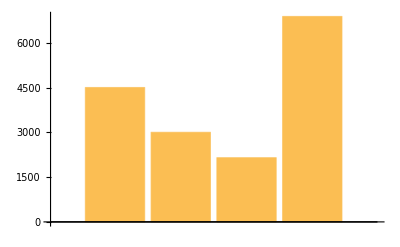

```mathematica
BarChart[alist]
```

```mathematica
blist = {{4500, 3000, 2150, 6879}, {6200, 1400, 2200, 8000}}
```

{{4500,3000,2150,6879},{6200,1400,2200,8000}}

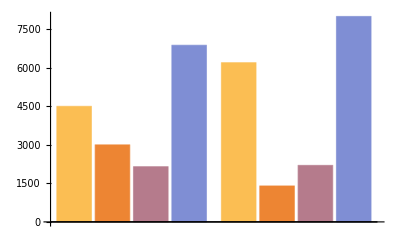

```mathematica
BarChart[blist]
```

```mathematica
clist = {{4500, 3000}, {2150, 6879}, {6200, 1400}, {2200, 800}}
```

{{4500,3000},{2150,6879},{6200,1400},{2200,800}}

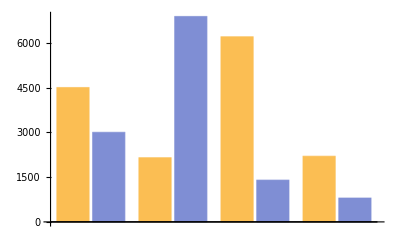

```mathematica
BarChart[clist]
```

```mathematica
blist = {1, 14, 19, 3, 7, 22, 16, 14}
```

{1,14,19,3,7,22,16,14}

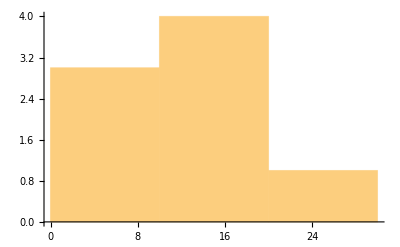

```mathematica
Histogram[blist]
```

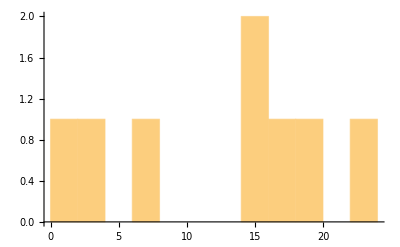

```mathematica
Histogram[blist, 22]
```

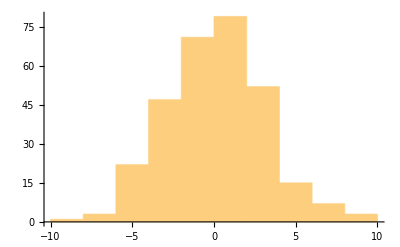

```mathematica
Histogram[RandomVariate[NormalDistribution[0, 3], 300]]
```

```mathematica
elist = {{14, 5}, {7, 7}, {4, 12}, {11, 6}}
```

{{14,5},{7,7},{4,12},{11,6}}

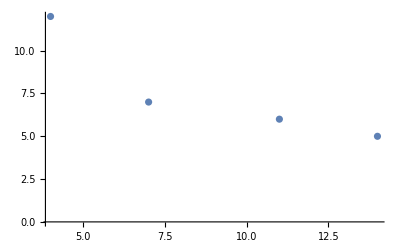

```mathematica
ListPlot[elist]
```

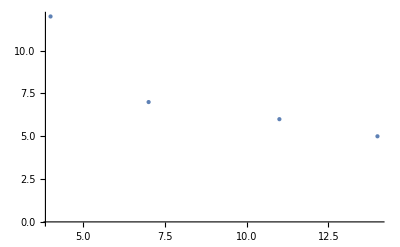

```mathematica
ListPlot[elist, PlotStyle -> PointSize[Large]]
```

```mathematica
alist = {14000, 2402, 5791}
blist = {7250, 4401, 3829}
```

{14000,2402,5791}

{7250,4401,3829}

```mathematica
PairedBarChart[alist, blist]
```

-Graphics-

```mathematica
clist = {Frequent, Occasional, Rare}
```

{Frequent,Occasional,Rare}

```mathematica
PairedBarChart[alist, blist, ChartLabels -> clist]
```

-Graphics-

```mathematica
blist = {7250, 4401, 3829}
```

{7250,4401,3829}

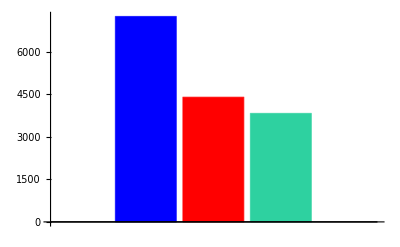

```mathematica
BarChart[blist, ChartStyle -> {Blue, Red, RGBColor[0.180392, 0.819608, 0.627451]}]
```

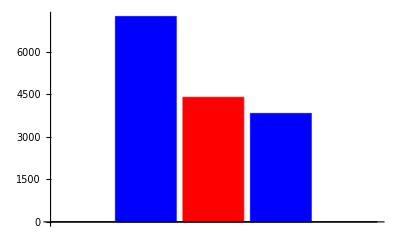

```mathematica
BarChart[blist, ChartStyle -> {Blue, Red}]
```

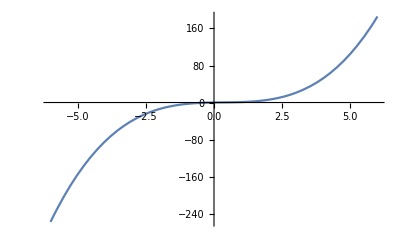

```mathematica
Plot[x^3 - x^2 + x, {x, -6, 6}]
```

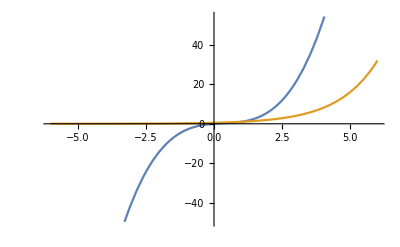

```mathematica
Plot[{x^3 - x^2 + x, 2^x - 2^(x - 1)}, {x, -6, 6}]
```

```mathematica
Manipulate[Plot[x^3 - a x^2 + a, {x, -6, 6}], {a, -15, 25}]
```

```mathematica
Manipulate[Plot[x^3 - a x^2 + a, {x, -6, 6}], {a, -15, 25, 5}]
```

```mathematica
Manipulate[Plot[x^3 - a x^2 + b, {x, -6, 6}], {a, -15, 25}, {b, 100, 1000}]
```

```mathematica
Animate[Plot[Cos[x + n], {x, 0, 20}], {n, 0, 10}, AnimationRunning -> False]
```